```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"]
```

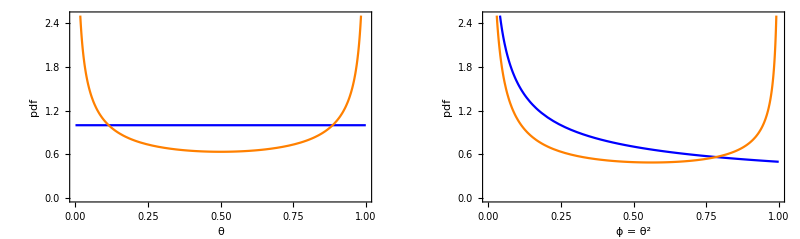

```mathematica
aDist=UniformDistribution[{0,1}];
cDist = BetaDistribution[0.5,0.5];
g1=Plot[{PDF[aDist,x],PDF[cDist,x]},{x,0,1},PlotStyle->{Blue,Orange},Frame->{True,True,False,False},FrameTicks->{True,True},FrameLabel->{"θ","pdf"},BaseStyle->{FontSize->16},PlotRange->{Automatic,{0,2.5}}];
bDist = TransformedDistribution[θ^2,θ\[Distributed]aDist];
dDist = TransformedDistribution[θ^2,θ\[Distributed]cDist];
g2=Plot[{PDF[bDist,x],PDF[dDist,x]},{x,0,1},PlotStyle->{Blue,Orange},Frame->{True,True,False,False},FrameTicks->{True,True},FrameLabel->{"ϕ = θ^2","pdf"},BaseStyle->{FontSize->16},PlotRange->{Automatic,{0,2.5}}];
gFinal=Show[GraphicsRow[{g1,g2}],ImageSize->800]
```

```mathematica
Integrate[PDF[bDist,x],{x,0,0.5}]
```

0.707107

```mathematica
Export["Objective_uniformPrior.pdf",gFinal]
```

Objective_uniformPrior.pdf